```mathematica
series=Import["/Users/peterkink/hopkins/COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
transeries=Transpose[series];
transeries=Drop[transeries,1];
Dimensions[transeries]
hopdates=Drop[series[[1]],4]
%//Length
countriescsv=transeries[[1]];
%//Dimensions
hopdatetodate[dstring_]:=ToExpression["{"<>StringReplace[dstring,"/"->","]<>"}"][[{3,1,2}]]+{2000,0,0}
```

{96,265}

{1/22/20,1/23/20,1/24/20,1/25/20,1/26/20,1/27/20,1/28/20,1/29/20,1/30/20,1/31/20,2/1/20,2/2/20,2/3/20,2/4/20,2/5/20,2/6/20,2/7/20,2/8/20,2/9/20,2/10/20,2/11/20,2/12/20,2/13/20,2/14/20,2/15/20,2/16/20,2/17/20,2/18/20,2/19/20,2/20/20,2/21/20,2/22/20,2/23/20,2/24/20,2/25/20,2/26/20,2/27/20,2/28/20,2/29/20,3/1/20,3/2/20,3/3/20,3/4/20,3/5/20,3/6/20,3/7/20,3/8/20,3/9/20,3/10/20,3/11/20,3/12/20,3/13/20,3/14/20,3/15/20,3/16/20,3/17/20,3/18/20,3/19/20,3/20/20,3/21/20,3/22/20,3/23/20,3/24/20,3/25/20,3/26/20,3/27/20,3/28/20,3/29/20,3/30/20,3/31/20,4/1/20,4/2/20,4/3/20,4/4/20,4/5/20,4/6/20,4/7/20,4/8/20,4/9/20,4/10/20,4/11/20,4/12/20,4/13/20,4/14/20,4/15/20,4/16/20,4/17/20,4/18/20,4/19/20,4/20/20,4/21/20,4/22/20,4/23/20}

93

{265}

```mathematica
TableForm[transeries];
```

```mathematica
countrynames={"Canada","Australia","New Zealand","Croatia","Czechia"};
```

```mathematica
countryparameters=
(*name,truncdrop,jp0,lag,projtime,bootlag,plotdrop*)
{{"Canada",200,{52180.39484847384,1005.9304582251706,0.1324225337960489},21,21,10,0},{"Australia",100,{6540.8364412808105,85.77223261633138,0.2345420078562459},21,21,10,0},{"New Zealand",5,{1441.2482649030032,14.971640930135235,0.23959274221723975},21,21,10,0},{"Croatia",10,{1985.7723787465545,21.596481176857367,0.1589401951808019},21,21,10,5},{"Czechia",10,{7096.988271837173,68.14371590582019,0.16461693785708748},21,21,10,5},
{"Singapore",200,{2.835279843883035*^8,64.38918662693713,0.1259411788554341},21,7,10,0},
{"Japan",1000,{17986.663577976567,576.9474735585374,0.12382285884487645},21,14,10,0}
}
```

{{Canada,200,{52180.4,1005.93,0.132423},21,21,10,0},{Australia,100,{6540.84,85.7722,0.234542},21,21,10,0},{New Zealand,5,{1441.25,14.9716,0.239593},21,21,10,0},{Croatia,10,{1985.77,21.5965,0.15894},21,21,10,5},{Czechia,10,{7096.99,68.1437,0.164617},21,21,10,5},{Singapore,200,{2.83528×10^8,64.3892,0.125941},21,7,10,0},{Japan,1000,{17986.7,576.947,0.123823},21,14,10,0}}

```mathematica
Export["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml",countryparameters]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml

```mathematica
countryparameters=Import["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml"]
```

{{Canada,200,{52180.4,1005.93,0.132423},21,21,10,0},{Australia,100,{6540.84,85.7722,0.234542},21,21,10,0},{New Zealand,5,{1441.25,14.9716,0.239593},21,21,10,0},{Croatia,10,{1985.77,21.5965,0.15894},21,21,10,5},{Czechia,10,{7096.99,68.1437,0.164617},21,21,10,5}}

```mathematica
countryparameters
```

{{Canada,200,{52180.4,1005.93,0.132423},21,21,10,0},{Australia,100,{6540.84,85.7722,0.234542},21,21,10,0},{New Zealand,5,{1441.25,14.9716,0.239593},21,21,10,0},{Croatia,10,{1985.77,21.5965,0.15894},21,21,10,5},{Czechia,10,{7096.99,68.1437,0.164617},21,21,10,5}}

```mathematica
SetDirectory["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump"]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump

country : Canada

data length : 40

start date : {2020,3,15}

April 24

Canadadate.txt

jdp0 : {52180.4,1005.93,0.132423}

jp20 : {80856.,2581.03,0.0886491}

backward result : {19758.,271.885,0.236761}

forward result : {80856.,2581.03,0.0886491}

last tab: {80856.,2581.03,0.0886491}

backward result : {19758.,271.885,0.236761}

forward result : {80856.,2581.03,0.0886491}

past errors : {{692.436,1051.57,2932.5,4308.12,5303.15,6107.74,7726.9,9123.85,11075.2,12461.3},6078.28}

boot tab : {{45958.,1054.91,0.134768},{40407.8,945.221,0.143658},{47853.4,1228.12,0.127235},{57811.7,1588.9,0.112084},{69239.7,1966.02,0.100293},{78771.6,2323.94,0.09197},{96797.3,2734.07,0.0835357},{120698.,3158.03,0.0763972},{181377.,3636.83,0.0690361},{229279.,3962.76,0.0651954}}

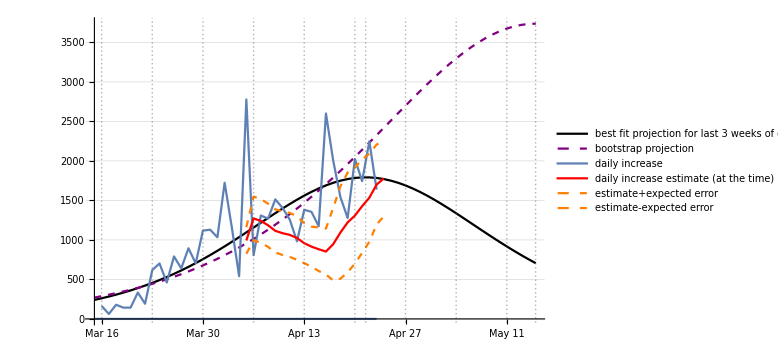

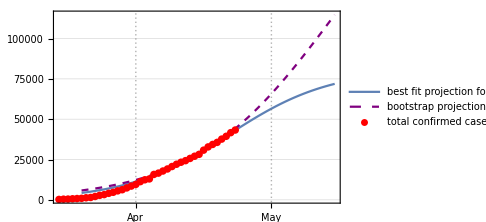

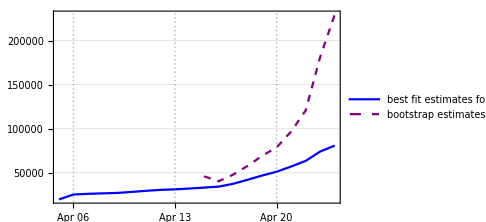

Canadagraf.png

Canadaloggraf.png

Canadadfgraf.png

Canadafinalplot.png

country : Australia

data length : 45

start date : {2020,3,10}

April 24

Australiadate.txt

jdp0 : {6540.84,85.7722,0.234542}

jp20 : {6742.97,568.264,0.149861}

backward result : {6333.48,61.3826,0.258068}

forward result : {6742.97,568.264,0.149861}

last tab: {6742.97,568.264,0.149861}

backward result : {6333.48,61.3826,0.258068}

forward result : {6742.97,568.264,0.149861}

past errors : {{85.2919,90.6797,97.0838,144.696,180.865,215.07,221.891,238.997,242.121,249.053},176.575}

boot tab : {{6236.05,65.0561,0.254921},{6538.97,99.7277,0.227185},{6680.96,127.765,0.212343},{6659.47,126.959,0.213015},{6685.33,145.069,0.206255},{6716.95,169.703,0.198415},{6739.39,206.803,0.189174},{6767.52,252.699,0.179859},{6868.31,385.44,0.159561},{6930.96,513.821,0.14614},{6988.52,689.771,0.132765},{6950.09,730.47,0.131633},{6956.65,930.089,0.122078},{7011.34,1279.75,0.10784},{7030.75,1582.12,0.0988361}}

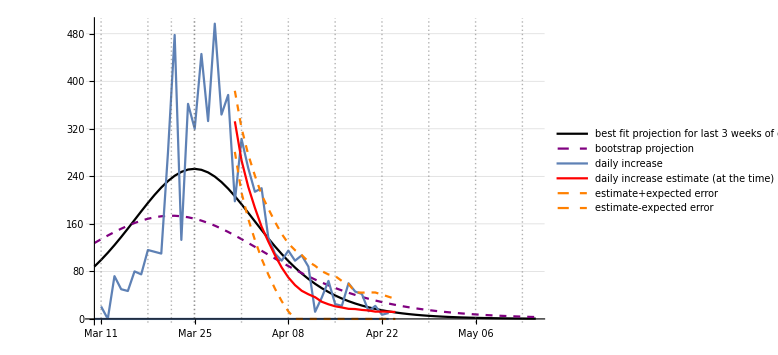

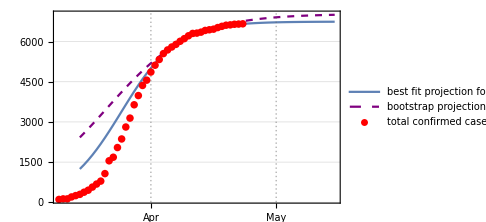

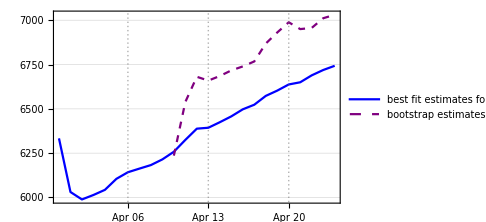

Australiagraf.png

Australialoggraf.png

Australiadfgraf.png

Australiafinalplot.png

country : New Zealand

data length : 41

start date : {2020,3,14}

April 24

New Zealanddate.txt

jdp0 : {1441.25,14.9716,0.239593}

jp20 : {1455.93,20.551,0.22275}

backward result : {981.19,4.49853,0.341492}

forward result : {1455.93,20.551,0.22275}

last tab: {1455.93,20.551,0.22275}

backward result : {981.19,4.49853,0.341492}

forward result : {1455.93,20.551,0.22275}

past errors : {{-0.595177,6.59481,11.2757,10.9912,17.3582,21.0591,25.8329,27.4672,30.7896,33.6614},18.4435}

boot tab : {{1833.01,53.1616,0.158085},{1745.34,52.5281,0.161741},{1653.58,49.0838,0.169019},{1584.85,44.396,0.177548},{1536.2,38.8581,0.18697},{1509.47,34.2446,0.194769},{1500.49,32.6958,0.197606},{1488.29,29.0462,0.2039},{1478.53,26.5983,0.208752},{1482.16,31.3381,0.201653},{1481.68,34.8448,0.197617}}

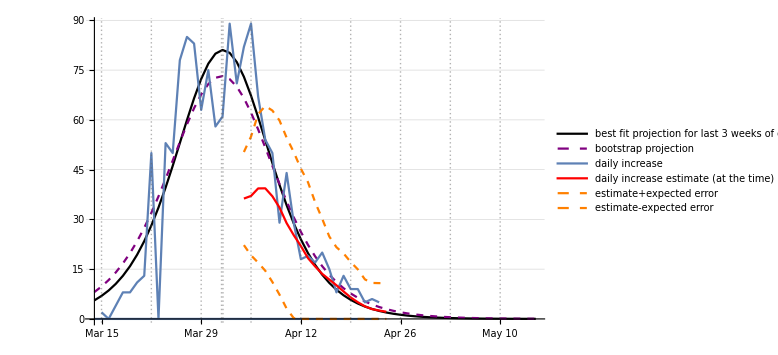

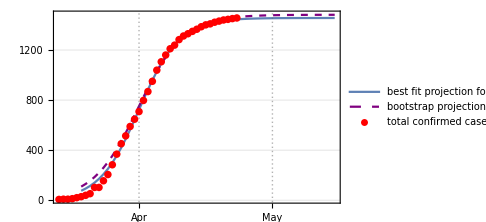

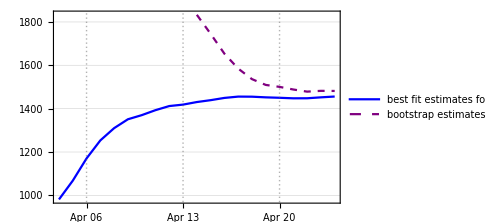

New Zealandgraf.png

New Zealandloggraf.png

New Zealanddfgraf.png

New Zealandfinalplot.png

country : Croatia

data length : 49

start date : {2020,3,6}

April 24

Croatiadate.txt

jdp0 : {1985.77,21.5965,0.15894}

jp20 : {2161.52,60.8519,0.120151}

backward result : {835.937,1.62704,0.316962}

forward result : {2161.52,60.8519,0.120151}

last tab: {2161.52,60.8519,0.120151}

backward result : {835.937,1.62704,0.316962}

forward result : {2161.52,60.8519,0.120151}

past errors : {{53.2863,58.7178,80.5335,78.4811,74.2996,93.7279,86.5118,98.4084,127.19,146.645},89.7801}

boot tab : {{1753.63,15.3017,0.178544},{1699.93,15.2697,0.179765},{1759.03,17.9074,0.171919},{1918.37,24.168,0.156701},{2031.8,30.4091,0.145864},{2234.16,41.1379,0.131574},{2212.36,46.4471,0.12736},{2419.65,61.3622,0.114706},{2598.91,77.5604,0.104611},{2869.15,98.1151,0.0943032},{3065.29,117.977,0.0868374},{3424.2,144.853,0.0782348},{3431.63,159.817,0.0751471},{3255.65,166.798,0.0748764},{3196.99,179.479,0.0731036},{2820.71,167.394,0.0783883},{2641.69,157.695,0.0823438},{2493.49,137.335,0.0886636},{2381.1,117.462,0.0953606}}

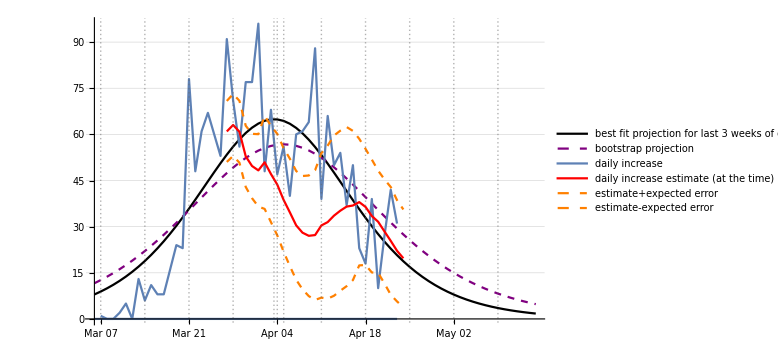

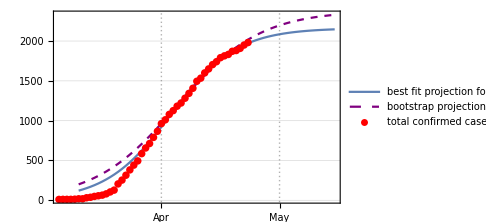

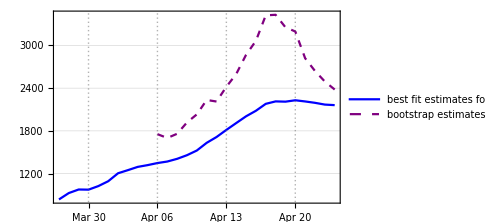

Croatiagraf.png

Croatialoggraf.png

Croatiadfgraf.png

Croatiafinalplot.png

country : Czechia

data length : 50

start date : {2020,3,5}

April 24

Czechiadate.txt

jdp0 : {7096.99,68.1437,0.164617}

jp20 : {7749.24,304.659,0.112303}

backward result : {2216.85,9.55805,0.303903}

forward result : {7749.24,304.659,0.112303}

last tab: {7749.24,304.659,0.112303}

backward result : {2216.85,9.55805,0.303903}

forward result : {7749.24,304.659,0.112303}

past errors : {{-73.9147,-60.2482,77.2959,124.441,121.972,210.761,320.769,416.062,482.8,510.241},213.018}

boot tab : {{9746.37,89.0792,0.147415},{8757.52,93.6428,0.147021},{7322.81,77.909,0.158933},{6079.92,47.0909,0.186442},{6848.02,73.7599,0.16362},{7931.86,112.511,0.142321},{8162.42,128.142,0.136611},{8321.56,143.242,0.131976},{8165.76,146.739,0.131839},{7956.08,149.669,0.132238},{7426.67,128.353,0.140741},{7457.47,143.195,0.137005},{7719.14,184.128,0.127089},{7803.91,208.119,0.122653},{7528.09,173.829,0.130412},{7492.7,175.735,0.130394},{7657.59,229.587,0.120863},{7980.6,340.932,0.106464},{8354.69,521.848,0.0914293},{8663.22,700.572,0.0810726}}

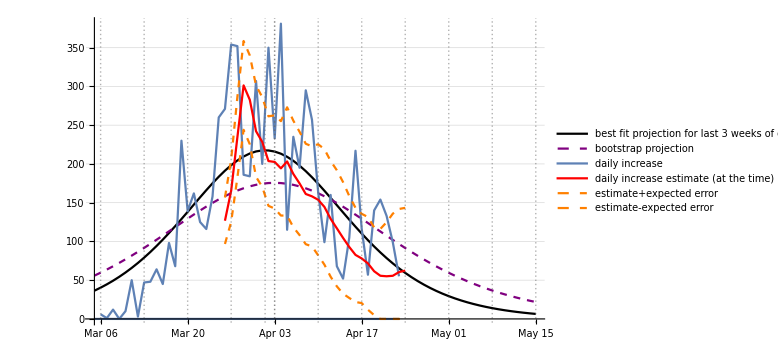

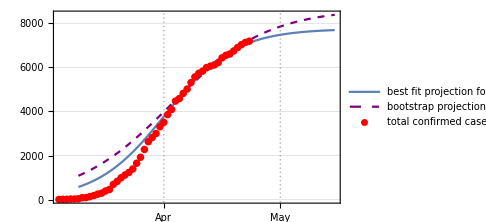

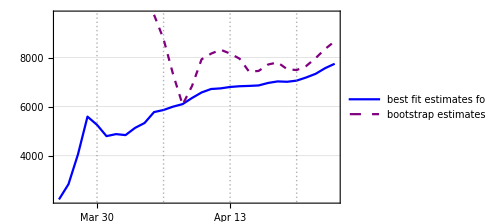

Czechiagraf.png

Czechialoggraf.png

Czechiadfgraf.png

Czechiafinalplot.png

country : Singapore

data length : 41

start date : {2020,3,14}

April 24

Singaporedate.txt

jdp0 : {2.83528×10^8,64.3892,0.125941}

jp20 : {2.83528×10^8,51.6871,0.13169}

backward result : {2.83528×10^8,231.105,0.0774476}

forward result : {2.83528×10^8,51.6871,0.13169}

last tab: {2.83528×10^8,51.6871,0.13169}

backward result : {2.83528×10^8,231.105,0.0774476}

forward result : {2.83528×10^8,51.6871,0.13169}

past errors : {{289.436,473.539,915.313,1226.69,1829.41,2056.03,3079.86,3753.01,4292.31,4810.31},2272.59}

boot tab : {{2.83528×10^8,173.182,0.0895698},{2.83528×10^8,148.858,0.0954217},{2.83528×10^8,125.707,0.101704},{2.83528×10^8,97.1074,0.111251},{2.83528×10^8,77.4353,0.118794},{2.83528×10^8,59.6598,0.127458},{2.83528×10^8,52.1201,0.131003},{2.83528×10^8,42.1004,0.137805},{2.83528×10^8,36.0406,0.142013},{2.83528×10^8,34.8225,0.142551},{2.83528×10^8,37.4544,0.140111}}

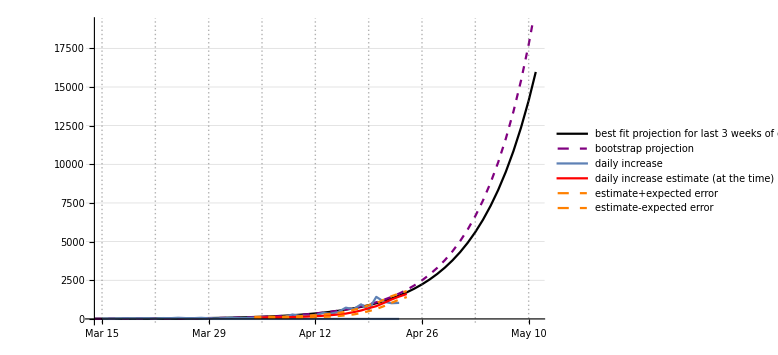

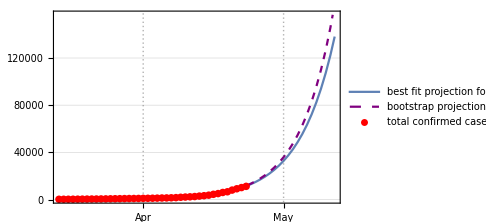

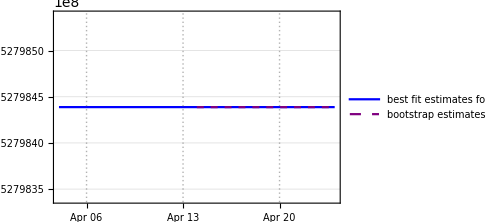

Singaporegraf.png

Singaporeloggraf.png

Singaporedfgraf.png

Singaporefinalplot.png

country : Japan

data length : 34

start date : {2020,3,21}

April 24

Japandate.txt

jdp0 : {17986.7,576.947,0.123823}

jp20 : {15093.,342.497,0.152687}

backward result : {1.5148×10^9,786.44,0.0899783}

forward result : {1.5148×10^9,1304.37,0.0681608}

last tab: {1.5148×10^9,1304.37,0.0681608}

backward result : {1.5148×10^9,786.44,0.0899783}

forward result : {1.5148×10^9,1304.37,0.0681608}

past errors : {{-357.464,-720.534,-1096.23,-929.109,-1515.59,-2222.05,-3552.95,-4681.9,-5921.81,-6848.},-2784.56}

boot tab : {{1.5148×10^9,1092.68,0.0758002},{1.5148×10^9,1345.52,0.067312},{1.5148×10^9,1684.89,0.0584298},{1.5148×10^9,1974.11,0.0526709}}

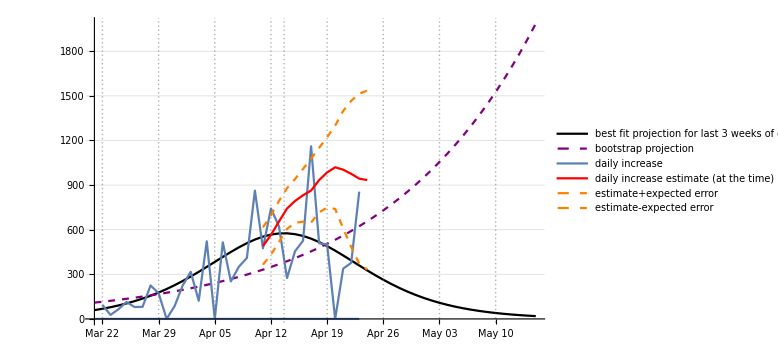

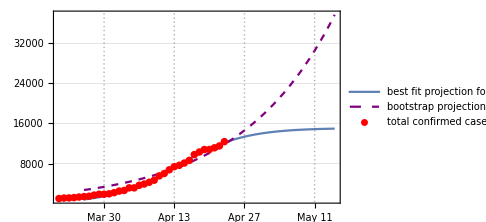

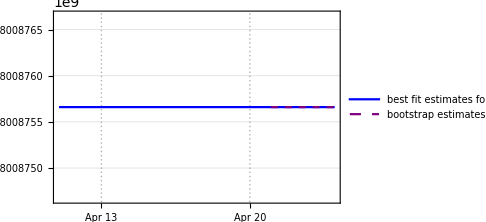

Japangraf.png

Japanloggraf.png

Japandfgraf.png

Japanfinalplot.png

{22.53845,Null}

```mathematica
countrydateplotlist={};
Timing[
For[cit=1,cit≤Length[countryparameters],cit++,
countrynames=Transpose[countryparameters][[1]];
currentnamme=countrynames[[cit]];
{currentnamme,ctrunc,jdp0,jlag,jprojtime,jbootlag,jplotdrop}=countryparameters[[cit]];
Print["country : ",currentnamme];
countinds=Flatten[Position[countriescsv,currentnamme]];
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}];

truncdatesandata=Select[datesanddata,#[[2]]>ctrunc&];
justdata=Transpose[truncdatesandata][[2]];
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]];
Print["data length : ",Length[justdata]];
Print["start date : ",jstartdate];

jdatestring=reldatetostring[cpstartdate,timecpert[[-1]]];
Print[jdatestring];
datefilename=currentnamme<>"date.txt";
Print[datefilename];
Export[datefilename,jdatestring];

{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime];
Print["jdp0 : ",jdp0];
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,jlag,justtime,{1,0}];
Print["jp20 : ",jp20];

(*update jdp0*)
countryparameters[[cit,3]]=jdp0;

{jgraf,jloggraf,jdfpplot,jprogplot,jfinal}=somegraphs[jdp0,jp20,justtime,justdata,jstartdate,21,21,5,10];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]];
Print[jgraf];
Print[jloggraf];
Print[jfinal];

graffilename=currentnamme<>"graf.png";
Export[graffilename,jgraf];
Print[graffilename];
loggraffilename=currentnamme<>"loggraf.png";
Export[loggraffilename,jloggraf];
Print[loggraffilename];
dfgraffilename=currentnamme<>"dfgraf.png";
Export[dfgraffilename,jdfpplot];
Print[dfgraffilename];
finalgraffilename=currentnamme<>"finalplot.png";
Export[finalgraffilename,jfinal];
Print[finalgraffilename];

countrydateplotlist=AppendTo[countrydateplotlist,datesanddata];
]
]
```

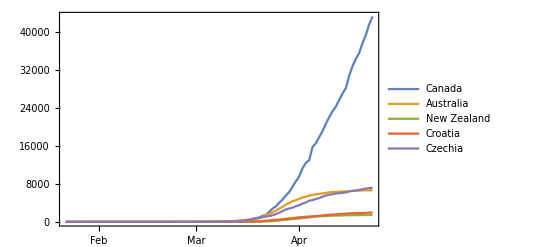

```mathematica
DateListPlot[countrydateplotlist,PlotLegends->countrynames,PlotRange->All]
```

```mathematica
countinds=Flatten[Position[countriescsv,"Japan"]]
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}]
```

{141}

{{{2020,1,22},2},{{2020,1,23},2},{{2020,1,24},2},{{2020,1,25},2},{{2020,1,26},4},{{2020,1,27},4},{{2020,1,28},7},{{2020,1,29},7},{{2020,1,30},11},{{2020,1,31},15},{{2020,2,1},20},{{2020,2,2},20},{{2020,2,3},20},{{2020,2,4},22},{{2020,2,5},22},{{2020,2,6},22},{{2020,2,7},25},{{2020,2,8},25},{{2020,2,9},26},{{2020,2,10},26},{{2020,2,11},26},{{2020,2,12},28},{{2020,2,13},28},{{2020,2,14},29},{{2020,2,15},43},{{2020,2,16},59},{{2020,2,17},66},{{2020,2,18},74},{{2020,2,19},84},{{2020,2,20},94},{{2020,2,21},105},{{2020,2,22},122},{{2020,2,23},147},{{2020,2,24},159},{{2020,2,25},170},{{2020,2,26},189},{{2020,2,27},214},{{2020,2,28},228},{{2020,2,29},241},{{2020,3,1},256},{{2020,3,2},274},{{2020,3,3},293},{{2020,3,4},331},{{2020,3,5},360},{{2020,3,6},420},{{2020,3,7},461},{{2020,3,8},502},{{2020,3,9},511},{{2020,3,10},581},{{2020,3,11},639},{{2020,3,12},639},{{2020,3,13},701},{{2020,3,14},773},{{2020,3,15},839},{{2020,3,16},839},{{2020,3,17},878},{{2020,3,18},889},{{2020,3,19},924},{{2020,3,20},963},{{2020,3,21},1007},{{2020,3,22},1101},{{2020,3,23},1128},{{2020,3,24},1193},{{2020,3,25},1307},{{2020,3,26},1387},{{2020,3,27},1468},{{2020,3,28},1693},{{2020,3,29},1866},{{2020,3,30},1866},{{2020,3,31},1953},{{2020,4,1},2178},{{2020,4,2},2495},{{2020,4,3},2617},{{2020,4,4},3139},{{2020,4,5},3139},{{2020,4,6},3654},{{2020,4,7},3906},{{2020,4,8},4257},{{2020,4,9},4667},{{2020,4,10},5530},{{2020,4,11},6005},{{2020,4,12},6748},{{2020,4,13},7370},{{2020,4,14},7645},{{2020,4,15},8100},{{2020,4,16},8626},{{2020,4,17},9787},{{2020,4,18},10296},{{2020,4,19},10797},{{2020,4,20},10797},{{2020,4,21},11135},{{2020,4,22},11512},{{2020,4,23},12368}}

```mathematica
truncdatesandata=Select[datesanddata,#[[2]]>1000&]
%//Length
justdata=Transpose[truncdatesandata][[2]]
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]]
```

{{{2020,3,21},1007},{{2020,3,22},1101},{{2020,3,23},1128},{{2020,3,24},1193},{{2020,3,25},1307},{{2020,3,26},1387},{{2020,3,27},1468},{{2020,3,28},1693},{{2020,3,29},1866},{{2020,3,30},1866},{{2020,3,31},1953},{{2020,4,1},2178},{{2020,4,2},2495},{{2020,4,3},2617},{{2020,4,4},3139},{{2020,4,5},3139},{{2020,4,6},3654},{{2020,4,7},3906},{{2020,4,8},4257},{{2020,4,9},4667},{{2020,4,10},5530},{{2020,4,11},6005},{{2020,4,12},6748},{{2020,4,13},7370},{{2020,4,14},7645},{{2020,4,15},8100},{{2020,4,16},8626},{{2020,4,17},9787},{{2020,4,18},10296},{{2020,4,19},10797},{{2020,4,20},10797},{{2020,4,21},11135},{{2020,4,22},11512},{{2020,4,23},12368}}

34

{1007,1101,1128,1193,1307,1387,1468,1693,1866,1866,1953,2178,2495,2617,3139,3139,3654,3906,4257,4667,5530,6005,6748,7370,7645,8100,8626,9787,10296,10797,10797,11135,11512,12368}

{2020,3,21}

```mathematica
jdp0={Max[justdata]2 ,500,0.20}
```

{24736,500,0.2}

```mathematica
{2.835279843883035*^8,247.73936265670633,0.12734516077629338}
```

{2.83528×10^8,247.739,0.127345}

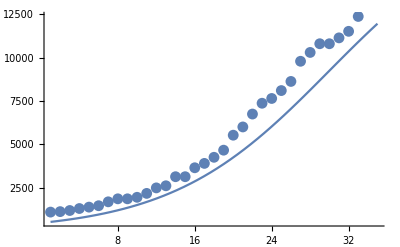

```mathematica
showplots[justdata,jdp0,justtime]
```

```mathematica
{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime]
```

{{17986.7,576.947,0.123823},10,3.35699×10^-7,34}

{15093.,342.497,0.152687}

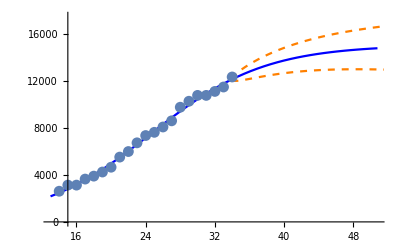
{-Graphics-,342.673,220.659,856,-9.35621,81.945}

```mathematica
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,21,justtime,{1,0}];
jp20
jpdata20=justdata[[-21;;]];
datastats[jpdata20,jp20,1.8,2,justtime[[-21;;]]]
```

```mathematica
estimates[justdata,jdp0,21,justtime];
```

backward result : {1.49161×10^9,829.83,0.0927027}

forward result : {1.49161×10^9,1396.38,0.0681608}

```mathematica
TableView[Transpose[generatestats[justdata,jdp0,21,justtime,jstartdate]]];
```

{981.19,4.49853,0.341492}

{1452.18,18.7219,0.227054}

{1452.18,18.7219,0.227054}

```mathematica
{"Japan",200,{17986.663577976567,576.9474735585374,0.12382285884487645},21,14,10,0}
```

backward result : {1.5148×10^9,786.44,0.0899783}

forward result : {1.5148×10^9,1304.37,0.0681608}

last tab: {1.5148×10^9,1304.37,0.0681608}

backward result : {1.5148×10^9,786.44,0.0899783}

forward result : {1.5148×10^9,1304.37,0.0681608}

past errors : {{-357.464,-720.534,-1096.23,-929.109,-1515.59,-2222.05,-3552.95,-4681.9,-5921.81,-6848.},-2784.56}

boot tab : {{1.5148×10^9,1092.68,0.0758002},{1.5148×10^9,1345.52,0.067312},{1.5148×10^9,1684.89,0.0584298},{1.5148×10^9,1974.11,0.0526709}}

April 24

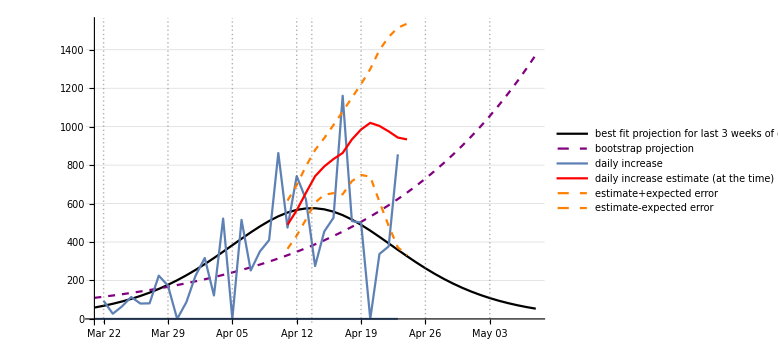

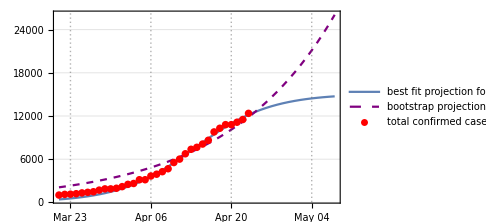

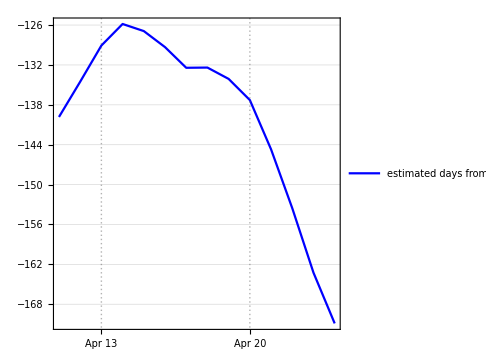

-Graphics-

```mathematica
{jgraf,jloggraf,jdfpplot,jprogplot,jfinal}=somegraphs[jdp0,jp20,justtime,justdata,jstartdate,21,14,0,10];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]]
jgraf
jloggraf
jdfpplot
jfinal
```

```mathematica
?somegraphs
```

Global`somegraphs

somegraphs[stp0_,fip0_,ttime_,tdata_,startdate_,lag_,projtime_,drop_]:=Module[{dailyincrease,stats,oneplot,erplot,projtimeinterval,dlplot,graf,logfunplot,cumdinplot,loggraf,dfpplot,progress,progplot,sifdate,sifplot,peakdate,fifdate,ticks,ests,esterrors,estminerrors,meanpasterrors,bootabctab,boottimewinds,bootdatelists,tabctab,twinds,dlbootplot,bootexpeakdate,bootabc,bootlogfunplot,bootplot,bestfitplot,pastfinalplot},dailyincrease=tdata⟦2;;-1⟧-tdata⟦1;;-2⟧;stats=generatestats[tdata,stp0,21,ttime,startdate];{tabctab,twinds}=estimates[tdata,stp0,lag,ttime];{meanpasterrors,bootabctab,boottimewinds,bootdatelists}=bootstrapestimates[tdata,stp0,ttime,lag,10,startdate,tabctab,twinds];bootabc=bootabctab⟦-1⟧;sifdate=DatePlus[startdate,plusd[fip0]-1];peakdate=DatePlus[startdate,expeak[fip0]-1];fifdate=DatePlus[startdate,minsd[fip0]-1];bootexpeakdate=DatePlus[startdate,expeak[bootabc]-1];Print[sifdate];oneplot=DateListPlot[dailyincrease,DatePlus[startdate,1],Joined→True,Axes→True,PlotLegends→{daily increase},PlotTheme→Detailed];ests=stats⟦1⟧;esterrors=stats⟦2⟧;estminerrors=ests-esterrors;estminerrors=(Max[0,#1]&)/@estminerrors;erplot=DateListPlot[{ests,ests+esterrors,estminerrors},DatePlus[startdate,lag],Axes→True,Joined→True,PlotStyle→{{Red},{Orange,Dashed},{Orange,Dashed}},PlotLegends→{daily increase estimate (at the time),estimate+expected error,estimate-expected error},PlotTheme→Detailed];projtimeinterval=Flatten[Append[ttime,Table[t,{t,ttime⟦-1⟧+1,ttime⟦-1⟧+projtime+1}]]];dlplot=DateListPlot[(dlfun[#1,fip0]&)/@projtimeinterval,startdate,PlotLegends→{best fit projection for last 3 weeks of data},PlotStyle→{Black},PlotTheme→Detailed];dlbootplot=DateListPlot[(dlfun[#1,bootabc]&)/@projtimeinterval,startdate,PlotLegends→{bootstrap projection},PlotStyle→{Purple,Dashed},PlotTheme→Detailed];ticks=Table[{DatePlus[startdate,i],DateString[DatePlus[startdate,i],{MonthNameShort, ,Day}],0.02,Blue},{i,ttime⟦1⟧,ttime⟦-1⟧+projtime,7}];ticks=AppendTo[ticks,{peakdate, ,0.05,Black}];ticks=AppendTo[ticks,{bootexpeakdate, ,0.05,Purple}];sifplot=DateListPlot[Table[0,{i,ttime⟦1⟧,ttime⟦-1⟧}],startdate,Ticks→{ticks,Automatic},Axes→True,Frame→False,PlotTheme→Detailed,FrameTicks→All,PlotStyle→Thick];projtimeinterval=Drop[projtimeinterval,drop];logfunplot=DateListPlot[(lfun[#1,fip0]&)/@projtimeinterval,DatePlus[startdate,drop],PlotLegends→{best fit projection for last 3 weeks of data},PlotTheme→Detailed];bootlogfunplot=DateListPlot[(lfun[#1,bootabc]&)/@projtimeinterval,DatePlus[startdate,drop],PlotLegends→{bootstrap projection},PlotTheme→Detailed,PlotStyle→{Purple,Dashed}];cumdinplot=DateListPlot[tdata,startdate,Joined→False,PlotLegends→{total confirmed cases},PlotStyle→{Red,PointSize[0.015]},PlotTheme→Detailed];loggraf=Show[logfunplot,bootlogfunplot,cumdinplot,ImageSize→Medium,PlotRange→All];dfpplot=DateListPlot[{-stats⟦4⟧},DatePlus[startdate,lag],PlotLegends→{estimated days from peak (at the time)},PlotStyle→{Blue,PointSize[0.01]},PlotTheme→Detailed,ImageSize→Medium,Axes→True,AspectRatio→1];progress=stats⟦5⟧;progplot=DateListPlot[{progress},DatePlus[startdate,lag],PlotLegends→{estimated progress (at the time)},PlotStyle→{Blue,PointSize[0.01]},PlotTheme→Detailed,PlotRange→All,AspectRatio→1];graf=Show[sifplot,dlplot,dlbootplot,oneplot,erplot,PlotRange→All,ImageSize→Large];bootplot=DateListPlot[Transpose[{bootdatelists,Transpose[bootabctab]⟦1⟧}],PlotStyle→{Purple,Dashed},PlotLegends→{bootstrap estimates for final number of cases (at the time)},PlotTheme→Detailed];bestfitplot=DateListPlot[Transpose[tabctab]⟦1⟧,DatePlus[startdate,ttime⟦lag⟧],PlotStyle→Blue,PlotLegends→{best fit estimates for final number of cases (at the time)},PlotTheme→Detailed];pastfinalplot=Show[bestfitplot,bootplot,PlotRange→All,ImageSize→Medium];{graf,loggraf,dfpplot,progplot,pastfinalplot}]